### Finding

```mathematica
$Assumptions=β>0 && σ > 0  &&Subscript[σ, γ]> 0 && x > β σ^2 / 2 &&  Element[{x, β,ω, σ,Subscript[σ, γ], Subscript[ν, 1], Subscript[ν, 2]},Reals] && 2x/β - σ^2 >= 0; 
 Exp[-(ω+x)^2/(2 Subscript[σ, γ]^2)]Exp[-(ω - Subscript[ν, 1])^2 / (4σ^2)]Exp[-(ω - Subscript[ν, 2])^2 / (4 σ^2)] / (σ Sqrt[2 Pi])
```

(ⅇ^(-(ω-ν_1)^2/(4 σ^2)-(ω-ν_2)^2/(4 σ^2)-(x+ω)^2/(2 σ_γ^2)))/(√(2 π) σ)

```mathematica
Integrate[%, {ω, -Infinity, Infinity}, Assumptions-> $Assumptions]
```

(ⅇ^(1/8 (-(2 ν_1^2)/σ^2-(2 ν_2^2)/σ^2+((ν_1/σ^2+ν_2/σ^2-(2 x)/σ_γ^2)^2)/(1/σ^2+1/σ_γ^2)-(4 x^2)/σ_γ^2)))/(σ √(1/σ^2+1/σ_γ^2))

```mathematica
Myexpr =Exp[ (Subscript[σ, γ]^2 σ^2((Subscript[ν, 1]+Subscript[ν, 2])/σ^2- (2x)/Subscript[σ, γ]^2)^2)/(8(σ^2 + Subscript[σ, γ]^2)) - x^2/(2 Subscript[σ, γ]^2) - (Subscript[ν, 1]+ Subscript[ν, 2])^2/(8σ^2)]
TheirExpr = Exp[-(Subscript[ν, 1]+ Subscript[ν, 2] + 2x)^2/(8(σ^2 + Subscript[σ, γ]^2))]
```

ⅇ^(-(ν_1+ν_2)^2/(8 σ^2)-x^2/(2 σ_γ^2)+(σ^2 ((ν_1+ν_2)/σ^2-(2 x)/σ_γ^2)^2 σ_γ^2)/(8 (σ^2+σ_γ^2)))

ⅇ^(-(2 x+ν_1+ν_2)^2/(8 (σ^2+σ_γ^2)))

```mathematica
FullSimplify[Myexpr == TheirExpr, Assumptions -> $Assumptions]
```

True

### Finding by integrating

```mathematica
$Assumptions=β>0 && s > 0 && σ > 0 && Element[{x,β,s, ω, ν, σ},Reals];
Sqrt[β / (4  Pi x)]Exp[-β( ν + 2x)^2 / (16x)];
```

```mathematica
Integrate[%,{x, β σ^2 / 2,β σ^2 / 2 + s^2/β}, Assumptions -> $Assumptions] // FullSimplify
```

1/2 (-Erf[(ν+β σ^2)/(2 √2 σ)]+Erf[(2 s^2+β (ν+β σ^2))/(2 √(4 s^2+2 β^2 σ^2))]+ⅇ^(-(β ν)/2) (-1+Erf[(2 s^2+β (-ν+β σ^2))/(2 √(4 s^2+2 β^2 σ^2))]+Erfc[(-ν+β σ^2)/(2 √2 σ)]))

```mathematica
Limit[%, s-> Infinity] // FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (ⅇ^(-(β ν)/2) Erfc[(-ν+β σ^2)/(2 √2 σ)]+Erfc[(ν+β σ^2)/(2 √2 σ)])

### Finding by integrating

```mathematica
$Assumptions=β>0 && σ > 0 && ε > 0 && Element[{x,β,s, ω, ν, σ, c,ε},Reals]&& s>c>0;
Exp[-(ω+x)^2/(2 (2x/β-σ^2))] / Sqrt[2Pi(2x/β-σ^2)]
```

(ⅇ^(-(x+ω)^2/(2 ((2 x)/β-σ^2))))/(√(2 π) √((2 x)/β-σ^2))

```mathematica
Integrate[%,{x,β σ^2/2,β σ^2/2+s^2/β},Assumptions->$Assumptions] // FullSimplify
```

1/2 ⅇ^(-1/4 β (β σ^2+2 ω+Abs[β σ^2+2 ω])) (1+Erf[s/2-(β Abs[β σ^2+2 ω])/(4 s)]+ⅇ^(1/2 β Abs[β σ^2+2 ω]) (-1+Erf[s/2+(β Abs[β σ^2+2 ω])/(4 s)])) (Assumptions→True)

```mathematica
Result = Limit[%, s-> Infinity] // FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

ⅇ^(-1/4 β (β σ^2+2 ω+Abs[β σ^2+2 ω])) (Assumptions→True)

```mathematica
PaperResult=Exp[-β ((ω + β σ^2 / 2)+Abs[(ω + β σ^2 / 2)])/2];
FullSimplify[Result == PaperResult, Assumptions -> $Assumptions]
```

(Assumptions→True)==1

```mathematica
Exp[-(ω+x)^2/(2 (2x/β-σ^2))] / Sqrt[2Pi(2x/β-σ^2)]
```

(ⅇ^(-(x+ω)^2/(2 ((2 x)/β-σ^2))))/(√(2 π) √((2 x)/β-σ^2))

```mathematica
Integrate[%,{x,β σ^2/2 + ε,β σ^2/2+s^2/β},Assumptions->$Assumptions] // FullSimplify
```

ConditionalExpression[1/2 (-Erf[1/4 √(β/ε) (2 ε+β σ^2+2 ω)]+Erf[(2 s^2+β^2 σ^2+2 β ω)/(4 s)]+ⅇ^(-1/2 β (β σ^2+2 ω)) (Erf[1/4 √(β/ε) (-2 ε+β σ^2+2 ω)]+Erf[s/2-(β (β σ^2+2 ω))/(4 s)])) (Assumptions→True), s^2≠β ε]

```mathematica
MetroEps = Limit[%, s-> Infinity] // FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

```mathematica
1/2 (ⅇ^(-1/2 β (β σ^2+2 ω)) (1+Erf[1/4 √(β/ε) (-2 ε+β σ^2+2 ω)])+Erfc[1/4 √(β/ε) (2 ε+β σ^2+2 ω)]) (Assumptions->True)
```

1/2 (ⅇ^(-1/2 β (β σ^2+2 ω)) (1+Erf[1/4 √(β/ε) (-2 ε+β σ^2+2 ω)])+Erfc[1/4 √(β/ε) (2 ε+β σ^2+2 ω)]) (Assumptions→True)

```mathematica
%/. {β->10, σ -> 1/10, ε-> 0.1}
```

1/2 (ⅇ^(-5 (1/10+2 ω)) (1+Erf[2.5 (-0.1+2 ω)])+Erfc[2.5 (0.3+2 ω)]) (Assumptions→True)

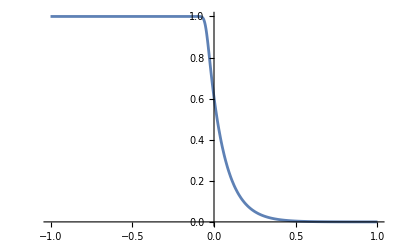

```mathematica
Plot[1/2 (ⅇ^(-5 (1/10+2 ω)) (1+Erf[25. (0.098+2 ω)])+Erfc[25. (0.10200000000000001+2 ω)]), {ω, -1.0, 1.0}]
```

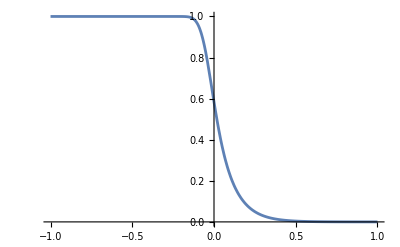

```mathematica
Plot[1/2 (ⅇ^(-5 (1/10+2 ω)) (1+Erf[7.905694150420948 (0.08+2 ω)])+Erfc[7.905694150420948 (0.12000000000000001+2 ω)]) ,{ω, -1.0, 1.0}]
```

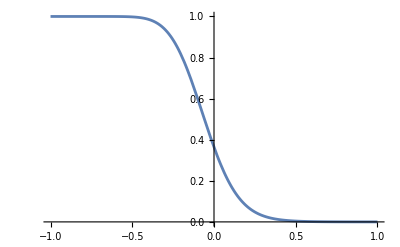

```mathematica
Plot[1/2 (ⅇ^(-5 (1/10+2 ω)) (1+Erf[2.5 (-0.1+2 ω)])+Erfc[2.5 (0.30000000000000004+2 ω)]) ,{ω, -1.0, 1.0}]
```

### Deriving from integrating

```mathematica
$Assumptions=β>0 && σ > 0  && Element[{β,ω, σ, Subscript[ν, 1], Subscript[ν, 2]},Reals]; 
Exp[-β ((ω + β σ^2 / 2)+Abs[(ω + β σ^2 / 2)])/2]Exp[-(ω - Subscript[ν, 1])^2 / (4σ^2)]Exp[-(ω - Subscript[ν, 2])^2 / (4 σ^2)] / (σ Sqrt[2 Pi])
```

(ⅇ^(-1/2 β ((β σ^2)/2+ω+Abs[(β σ^2)/2+ω])-(ω-ν_1)^2/(4 σ^2)-(ω-ν_2)^2/(4 σ^2)))/(√(2 π) σ)

```mathematica
Integrate[%, {ω, -Infinity, Infinity}, Assumptions-> $Assumptions]
```

1/2 ⅇ^(-ν_1^2/(8 σ^2)-(ν_1 (4 β σ^2-2 ν_2))/(8 σ^2)-(ν_1-ν_2)^2/(8 σ^2)-(ν_2 (4 β σ^2+ν_2))/(8 σ^2)) (ⅇ^((ν_1-ν_2)^2/(8 σ^2)) Erfc[(β σ^2-ν_1-ν_2)/(2 √2 σ)]+ⅇ^(ν_1^2/(8 σ^2)+(ν_1 (4 β σ^2-2 ν_2))/(8 σ^2)+(ν_2 (4 β σ^2+ν_2))/(8 σ^2)) Erfc[(β σ^2+ν_1+ν_2)/(2 √2 σ)])

```mathematica
MyAlphaMetroFromGamma = FullSimplify[%, Assumptions->$Assumptions]
```

1/2 ⅇ^(-(ν_1^2+ν_1 (4 β σ^2-2 ν_2)+ν_2 (4 β σ^2+ν_2))/(8 σ^2)) (Erfc[(β σ^2-ν_1-ν_2)/(2 √2 σ)]+ⅇ^(1/2 β (ν_1+ν_2)) Erfc[(β σ^2+ν_1+ν_2)/(2 √2 σ)])

```mathematica
PaperAlphaMetro = 0.5 Exp[-(Subscript[ν, 1] - Subscript[ν, 2])^2 / (8 σ^2)](Erfc[(β σ)/Sqrt[8] + (Subscript[ν, 1]+Subscript[ν, 2])/(Sqrt[8]σ)] + Exp[(-β(Subscript[ν, 1]+Subscript[ν, 2]))/2]Erfc[(β σ)/Sqrt[8] - (Subscript[ν, 1]+Subscript[ν, 2])/(Sqrt[8]σ)])
```

0.5 ⅇ^(-(ν_1-ν_2)^2/(8 σ^2)) (ⅇ^(-1/2 β (ν_1+ν_2)) Erfc[(β σ)/(2 √2)-(ν_1+ν_2)/(2 √2 σ)]+Erfc[(β σ)/(2 √2)+(ν_1+ν_2)/(2 √2 σ)])

```mathematica
FullSimplify[MyAlphaMetroFromGamma == PaperAlphaMetro, Assumptions -> $Assumptions]
```

True

```mathematica
$Assumptions=β>0 && σ > 0  && Element[{β,ω, σ, Subscript[ν, 1], Subscript[ν, 2]},Reals]; 
Exp[-(ω - Subscript[ν, 1])^2 / (4σ^2)]Exp[-(ω - Subscript[ν, 2])^2 / (4 σ^2)] / (σ Sqrt[2 Pi])
```

(ⅇ^(-(ω-ν_1)^2/(4 σ^2)-(ω-ν_2)^2/(4 σ^2)))/(√(2 π) σ)

```mathematica
Integrate[%, {ω, -Infinity, Infinity}, Assumptions-> $Assumptions]
```

ⅇ^(-(ν_1-ν_2)^2/(8 σ^2))

```mathematica
Subscript[ν, 1] = 0.172; Subscript[ν, 2] = -0.086; β = 10.0; σ = 1/10.0
```

0.1

```mathematica
$Assumptions=β>0 && σ > 0  && Element[{β,ω, σ, Subscript[ν, 1], Subscript[ν, 2]},Reals]; 
Exp[-β ((ω + β σ^2 / 2)+Abs[(ω + β σ^2 / 2)])/2]Exp[-(ω - Subscript[ν, 1])^2 / (4σ^2)]Exp[-(ω - Subscript[ν, 2])^2 / (4 σ^2)] / (σ Sqrt[2 Pi])
```

3.98942 ⅇ^(-25. (-0.172+ω)^2-25. (0.086+ω)^2-5. (0.05+ω+Abs[0.05+ω]))

```mathematica
Integrate[%, {ω, -Infinity, Infinity}, Assumptions-> $Assumptions]
```

0.210306

```mathematica
Subscript[ν, 1] = -0.45; Subscript[ν, 2]=-0.45; σ = 1/β;
AlphaMBeforeInt = Exp[-(ω - Subscript[ν, 1])^2 / (4σ^2)]Exp[-(ω - Subscript[ν, 2])^2 / (4 σ^2)] / (σ Sqrt[2 Pi])
```

(ⅇ^(-1/2 β^2 (0.45+ω)^2) β)/(√(2 π))

```mathematica
Reduce[{AlphaMBeforeInt< ε,0<ε< 10^-10 ,ω <= -0.45, β > 0}, ω, Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(((0<β<2.50663×10^-10&&0<ε≤0.398942 β)||(β==2.50663×10^-10&&0<ε<1.×10^-10)||(β>2.50663×10^-10&&0<ε<1.×10^-10))&&ω<-0.45-1.41421 √(-(1. Log[(2.50663 ε)/β])/β^2))||(0<β<2.50663×10^-10&&0.398942 β<ε<1.×10^-10&&ω≤-0.45)

```mathematica
Subscript[ν, 1] = 0.45; Subscript[ν, 2]=0.45; σ = 1/β;
AlphaMBeforeInt = Exp[-β ((ω + β σ^2 / 2))]Exp[-(ω - Subscript[ν, 1])^2 / (4σ^2)]Exp[-(ω - Subscript[ν, 2])^2 / (4 σ^2)] / (σ Sqrt[2 Pi])
```

(ⅇ^(-1/2 β^2 (-0.45+ω)^2-β (1/(2 β)+ω)) β)/(√(2 π))

```mathematica
Reduce[{AlphaMBeforeInt< ε,0<ε< 10^-10 ,ω >= 0.45, β > 0}, ω, Reals]
```

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

Reduce[{(ⅇ^(-1/2 β^2 (-0.45+ω)^2-β (1/(2 β)+ω)) β)/(√(2 π))<ε,0<ε<1/10000000000,ω≥0.45,β>0},ω,ℝ]

```mathematica
Exprr = 1/2 β^2(-9/20 + ω)^2 + β(1/(2β)+ω) + Log[Sqrt[2Pi]/β ϵ];
Reduce[{Exprr <= 0,Element[{β,ω, ϵ},Reals] && β > 0 && 0< ϵ < 1}, ω, Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{1/2 β^2 (-9/20+ω)^2+β (1/(2 β)+ω)+Log[(√(2 π) ϵ)/β]≤0,(β|ω|ϵ)∈ℝ&&β>0&&0<ϵ<1},ω,ℝ]

### b1, b2

```mathematica
$Assumptions=β>0 && σ > 0  && Element[{β,ω, σ, Subscript[ν, 1], Subscript[ν, 2], ν, x, t},Reals] && x >= β σ^2/2; Exp[(-(ν + 2x)^2)/(16x/β)]Exp[I ν t] / Sqrt[2 Pi]
```

(ⅇ^(ⅈ t ν-(β (2 x+ν)^2)/(16 x)))/(√(2 π))

```mathematica
Integrate[%, {ν, -Infinity, Infinity} , Assumptions -> $Assumptions]
```

2 √2 ⅇ^(-2 t x (ⅈ+(2 t)/β)) √(x/β)

```mathematica
Sinh[-β ν / 4]/(2 I)Exp[-ν^2/(8σ^2)]Exp[I ν t] / Sqrt[2 Pi]
```

(ⅈ ⅇ^(ⅈ t ν-ν^2/(8 σ^2)) Sinh[(β ν)/4])/(2 √(2 π))

```mathematica
Integrate[%, {ν, -Infinity, Infinity} , Assumptions -> $Assumptions]
```

1/2 ⅈ ⅇ^(-1/8 (4 t+ⅈ β)^2 σ^2) (-1+ⅇ^(2 ⅈ t β σ^2)) σ

```mathematica
1/(2Pi Cosh[-β ν / 4])Exp[I ν t] / Sqrt[2 Pi]
```

(ⅇ^(ⅈ t ν) Sech[(β ν)/4])/(2 √2 π^(3/2))

```mathematica
Integrate[%, {ν, -Infinity, Infinity} , Assumptions -> $Assumptions]
```

(√(2/π) Sech[(2 π t)/β])/β

```mathematica
β = 10.0; σ = 1/β;
FPlusMetro = 1/2(Erfc[(β σ^2 + ν)/Sqrt[8]] + Exp[-β ν / 2]Erfc[(β σ^2 - ν)/Sqrt[8]]) - (1- ν/Abs[ν])/4
```

1/4 (-1+ν/Abs[ν])+1/2 (ⅇ^(-5. ν) Erfc[(0.1-ν)/(2 √2)]+Erfc[(0.1+ν)/(2 √2)])

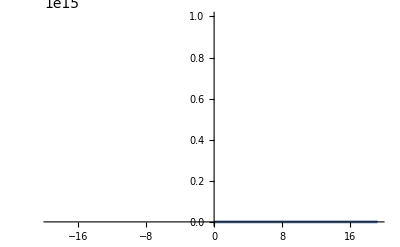

```mathematica
Plot[FPlusMetro,{ν,-19.19042206135785,19.16542206135785}]
```

```mathematica
Plot[FPlusMetro,{ν,-26.380844122715704,26.330844122715703}]
```

-Graphics-

```mathematica
$Assumptions = η>0 && β>0 && σ && Element[{ σ, ν, t, β},Reals];
B2Metro = 1/(4Sqrt[2]Pi)(Exp[(-2t^2 -I t)] + Boole[Abs[t]<=η]I(2t+I))/(t(2t + I))
```

(ⅇ^(-ⅈ t-2 t^2)+ⅈ (ⅈ+2 t) Boole[Abs[t]≤η])/(4 √2 π t (ⅈ+2 t))

```mathematica
ν = 0.1; η = 0.02; 
NIntegrate[B2Metro Exp[-I ν t] / Sqrt[2 Pi], {t, -Infinity, Infinity}]
```

0.01442+8.55913×10^-15 ⅈ

```mathematica
$Assumptions = η>0 && β>0 && σ && Element[{ σ, ν, t, β},Reals];
FPlusNu[ν_] := 1/2(Erfc[(β σ^2 + ν)/Sqrt[8]] + Exp[-β ν / 2] Erfc[(β σ^2 - ν)/Sqrt[8]])
```

1/2 (ⅇ^(-(β ν)/2) Erfc[(-ν+β σ^2)/(2 √2)]+Erfc[(ν+β σ^2)/(2 √2)])

```mathematica
Integrate[FPlusNu * Exp[I ν t] / Sqrt[2 Pi], {ν, -Infinity, Infinity} , Assumptions->$Assumptions]
```

$Aborted

### Factor 2

```mathematica
$Assumptions = β>0 && σ > 0&& Element[{ s, ω, σ, ν, t, β},Reals];
ft = Exp[-σ^2 t^2] Sqrt[σ Sqrt[2 / Pi]];
Fw = Exp[-ω^2/(4 σ^2)] / Sqrt[2 σ Sqrt[2 Pi]];
```

```mathematica
ftFourier = Integrate[ft *  Exp[-I ω t] / Sqrt[2 Pi], {t, -Infinity, Infinity}, Assumptions->$Assumptions ]
```

(ⅇ^(-ω^2/(4 σ^2)))/((2 π)^(1/4) √σ)

```mathematica
FullSimplify[Fw == ftFourier, Assumptions->$Assumptions]
```

False

```mathematica
$Assumptions = s> 0 && β>0 && σ > 0&& Element[{ s, ω, σ, ν, t, β},Reals];
```

```mathematica
Limit[(-Exp[(-4 t^2 s^2)/β^2 - (2 I t s^2)/β])/(t(2t/β + I) / beta), s->Infinity, Assumptions->$Assumptions]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

Limit[-(beta ⅇ^(-(4 s^2 t^2)/β^2-(2 ⅈ s^2 t)/β))/(t (ⅈ+(2 t)/β)),s→∞,Assumptions→s>0&&β>0&&σ>0&&(s|ω|σ|ν|t|β)∈ℝ]

```mathematica
FNuZero =  1/2(Erfc[(β σ^2 + ν)/Sqrt[8]] + Exp[-β ν / 2] Erfc[(β σ^2 - ν)/Sqrt[8]]) - (1 - Sign[ν])/4
```

1/2 (ⅇ^(-(β ν)/2) Erfc[(-ν+β σ^2)/(2 √2)]+Erfc[(ν+β σ^2)/(2 √2)])+1/4 (-1+Sign[ν])

```mathematica
Integrate[FNuZero/Sqrt[2 Pi] Exp[I ν t], {ν, -Infinity, Infinity}, Assumptions->$Assumptions]
```

Integrate[(ⅇ^(ⅈ t ν) (1/2 (ⅇ^(-(β ν)/2) Erfc[(-ν+β σ^2)/(2 √2)]+Erfc[(ν+β σ^2)/(2 √2)])+1/4 (-1+Sign[ν])))/(√(2 π)),{ν,-∞,∞},Assumptions→s>0&&β>0&&σ>0&&(s|ω|σ|ν|t|β)∈ℝ]

```mathematica
$Assumptions = s> 0 && β>0 && σ > 0&& Element[{ s, ω, σ, ν, t, β},Reals];
```

```mathematica
Integrate[2/Sqrt[2Pi] Exp[(-4 t^2 x)/β-2I t x], x, Assumptions->$Assumptions]
```

-(ⅇ^(-(2 t x (2 t+ⅈ β))/β) β)/(√(2 π) t (2 t+ⅈ β))

```mathematica
tPlus = (Exp[-2t^2 - I t] + I (2 t + I))/(t(2 t + I))
```

(ⅇ^(-ⅈ t-2 t^2)+ⅈ (ⅈ+2 t))/(t (ⅈ+2 t))

```mathematica
Limit[tPlus, t-> 0]
```

1

```mathematica
$Assumptions = s> 0 && β>0 && σ > 0&& Element[{ s, ω, σ, ν, t, β},Reals];
```

```mathematica
Fnu0 = 1/2(Erfc[(β σ^2 + ν)/Sqrt[8]] + Exp[-β ν / 2] Erfc[(β σ^2 - ν)/Sqrt[8]]) - (1 - Sign[ν])/2
```

```mathematica
1/2 (ⅇ^(-(β ν)/2) Erfc[(-ν+β σ^2)/(2 √2)]+Erfc[(ν+β σ^2)/(2 √2)])+1/2 (-1+Sign[ν])
```

1/2 (ⅇ^(-(β ν)/2) Erfc[(-ν+β σ^2)/(2 √2)]+Erfc[(ν+β σ^2)/(2 √2)])+1/2 (-1+Sign[ν])

```mathematica
NIntegrate[Fnu0/Sqrt[2 Pi] Exp[I ν t], {ν, -100.0, -0.001}]
```

NIntegrate::inumr: The integrand (ⅇ^(ⅈ t ν) (1/2 (ⅇ^(-(β ν)/2) Erfc[1/2 Power[«2»] Plus[«2»]]+Erfc[(ν+Times[«2»])/(2 √2)])+1/2 (-1+Sign[ν])))/(√(2 π)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-100.,-0.001}}.

NIntegrate[(Fnu0 Exp[ⅈ ν t])/(√(2 π)),{ν,-100.,-0.001}]